# 3-band chiral flattened: self-consistency, Ds and Tc

### Def: bloch state

```mathematica
a[J_,m_,k_,phi_]:=k^J Cos[J phi]
```

```mathematica
b[J_,m_,k_,phi_]:=k^J Sin[J phi]
```

Bloch states:

```mathematica
uplus[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I a[J,m,k,phi]m}
```

```mathematica
uplusdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I a[J,m,k,phi]m}
```

```mathematica
u0[J_,m_,k_,phi_]:=(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(-1/2){-b[J,m,k,phi],I m,a[J,m,k,phi]}
```

```mathematica
u0dag[J_,m_,k_,phi_]:=(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(-1/2){-b[J,m,k,phi],-I m,a[J,m,k,phi]}
```

```mathematica
uminus[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){-a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,-b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I a[J,m,k,phi]m}
```

```mathematica
uminusdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){-a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,-b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I a[J,m,k,phi]m}
```

### Def: quasiparticle energy

quasiparticle band at μ=0:

```mathematica
quasiplusf[m_,delta_]:=Sqrt[m^2+delta^2]
```

```mathematica
quasi0f[m_,delta_]:=delta
```

```mathematica
quasiminusf[m_,delta_]:=Sqrt[m^2+delta^2]
```

## secant to solve gap equation

### Def: gap eq at T=0

compute U from the gap equation

```mathematica
uaf[J_,m_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2/(2quasiplusf[m,delta])+Abs[u0[J,m,k,phi][[1]]]^2/(2quasi0f[m,delta])+Abs[uminus[J,m,k,phi][[1]]]^2/(2quasiminusf[m,delta])),{phi,0,2π},{k,0,1}];
1/integral
)
```

```mathematica
ubf[J_,m_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2/(2quasiplusf[m,delta])+Abs[u0[J,m,k,phi][[2]]]^2/(2quasi0f[m,delta])+Abs[uminus[J,m,k,phi][[2]]]^2/(2quasiminusf[m,delta])),{phi,0,2π},{k,0,1}];
1/integral
)
```

### calculation

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(i-1)+0.0001,{i,1,51}];
ualist={};
ublist={};
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=uaf[J,m];
ubvalue=ubf[J,m];
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
];
dataA=Table[{mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
```

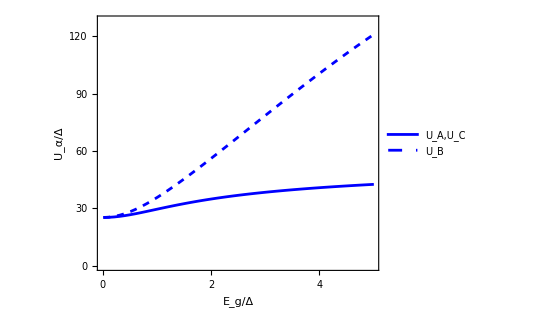

```mathematica
small3bandf=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,128}},
PlotStyle->{Blue,{Blue,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,
FrameTicks->{{{0,30,60,90,120},None},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ","U_α/Δ"},
PlotLegends->Placed[LineLegend[{Style["U_A,U_C",15],Style["U_B",15]},LegendLayout->"Row"], {0.5,0.13}],
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
J=1;delta=0.1;
mlist=Table[0.01(i-1)+0.001,{i,1,51}];
ualist={};
ublist={};
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=uaf[J,m];
ubvalue=ubf[J,m];
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
];
dataA=Table[{mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
```

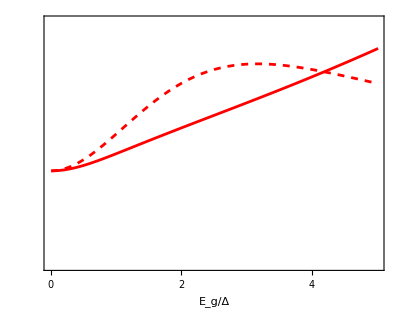

```mathematica
large3bandf=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,65}},
PlotStyle->{Red,{Red,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,FrameTicks->{{None,{0,20,40,60}},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ",""},
(*PlotLegends->Placed[{"U_A","U_B"}, {0.3,0.8}],*)
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
uplot3bandf=Overlay[{small3bandf,large3bandf}]
```

-Graphics--Graphics-

```mathematica
Export["3bandUf.pdf",uplot3bandf]
```

3bandUf.pdf

### Def: secant method solve Δ from fixed U_A, U_B at finite T

```mathematica
newtonA3bandf[deltaA_?NumericQ,deltaB_?NumericQ,temp_,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
integral=(uA/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2 Tanh[quasiplusf[m,deltaavg]/(2temp)]/(2quasiplusf[m,deltaavg])+Abs[u0[J,m,k,phi][[1]]]^2Tanh[quasi0f[m,deltaavg]/(2temp)]/(2quasi0f[m,deltaavg])+Abs[uminus[J,m,k,phi][[1]]]^2Tanh[quasiminusf[m,deltaavg]/(2temp)]/(2quasiminusf[m,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaA
)
```

```mathematica
newtonB3bandf[deltaA_?NumericQ,deltaB_?NumericQ,temp_,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
integral=(uB/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2 Tanh[quasiplusf[m,deltaavg]/(2temp)]/(2quasiplusf[m,deltaavg])+Abs[u0[J,m,k,phi][[2]]]^2Tanh[quasi0f[m,deltaavg]/(2temp)]/(2quasi0f[m,deltaavg])+Abs[uminus[J,m,k,phi][[2]]]^2Tanh[quasiminusf[m,deltaavg]/(2temp)]/(2quasiminusf[m,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaB
)
```

```mathematica
secant3bandfstep[{deltaA0_,deltaB0_},{deltaA1_,deltaB1_}]:=(
input0={deltaA0,deltaB0};
input1={deltaA1,deltaB1};
functionlist={newtonA3bandf,newtonB3bandf};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],temp,uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],temp,uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],temp,uA,uB],{k,1,2}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
secant3bandf[inputdeltaA_,inputdeltaB_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB};
outputlist0=outputlist1+0.001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.95,secant3bandfstep[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
)
```

### example calculation

m=0 is always uniform

```mathematica
J=1;mvalue=0;delta=0.1;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
temp=0.0001;m=0;
secant3bandf[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.,Null}

damping factor is 1.

deltas are {0.1,0.1}

```mathematica
J=1;mvalue=0;delta=0.1;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
temp=0.01;m=0;
secant3bandf[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.109375,Null}

damping factor is 0.999871

deltas are {0.0999909,0.0999909}

as m becomes larger

```mathematica
J=1;mvalue=0;delta=0.1;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
temp=0.01;m=0.1;
secant3bandf[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.046875,Null}

damping factor is 0.972986

deltas are {0.0783597,0.0606502}

```mathematica
J=1;mvalue=0;delta=0.1;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
temp=0.01;m=0.3;
secant3bandf[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.078125,Null}

damping factor is 0.980586

deltas are {0.0460091,0.0324103}

```mathematica
J=1;mvalue=0;delta=0.1;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
temp=0.01;m=0.5;
secant3bandf[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.03125,Null}

damping factor is 0.975903

deltas are {0.0335997,0.0426999}

### Def: show how uniform as E_g and T changes

```mathematica
howuniform3bandf[mstep_,mlength_,tempstep_,templength_]:=(
mvalue=0;(*J and delta are given outside, to use function uA and uB*)
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
mlist=Table[mstep(i-1),{i,1,mlength}];
templist=Table[tempstep(i-1)+0.0001,{i,1,templength}];
deltaavgtable=ConstantArray[0,{mlength,templength}];
deltaratiotable=ConstantArray[0,{mlength,templength}];
(*{deltaA,deltaB}={delta,delta};*)
For[iofm=1,iofm<mlength+1,iofm++,
m=mlist[[iofm]];
For[ioftemp=1,ioftemp<templength+1,ioftemp++,
temp=templist[[ioftemp]];
secant3bandf[delta,delta];(*use previous output as new input to save iteration steps*)
deltaavgtable[[iofm,ioftemp]]=(2deltaA+deltaB)/3;
deltaratiotable[[iofm,ioftemp]]=deltaA/deltaB;
];
];
)
```

### Δ=0.1 calculation***

```mathematica
J=1;delta=0.1;
mstep=0.05;mlength=11;tempstep=0.004;templength=15;
howuniform3bandf[mstep,mlength,tempstep,templength]//Timing
```

{345.188,Null}

```mathematica
deltaavg3dplot01=ListPlot3D[Flatten[Table[{mlist[[i]],templist[[j]],deltaavgtable[[i,j]]},{i,1,mlength},{j,1,templength}],1],
AxesLabel->{"E_g/ε_Λ","T/ε_Λ","Δ̄"},
LabelStyle->Directive[Black,15],
Mesh->Full,Boxed->False,ViewPoint->{1.5,-1,1},
ImageSize->300]
```

-Graphics3D-

```mathematica
Export["avg3dplot01.pdf",deltaavg3dplot01]
```

avg3dplot01.pdf

```mathematica
deltaratio3dplot01=ListPlot3D[Flatten[Table[{mlist[[i]],templist[[j]],deltaratiotable[[i,j]]},{i,1,mlength},{j,1,templength}],1],
PlotRange->{0,1.8},
AxesLabel->{"E_g/ε_Λ","T/ε_Λ","Δ_A/Δ_B"},
LabelStyle->Directive[Black,15],
Mesh->Full,Boxed->False,ViewPoint->{1.5,-1,1},
ImageSize->300]
```

-Graphics3D-

```mathematica
Export["ratio3dplot01.pdf",deltaratio3dplot01]
```

ratio3dplot01.pdf

```mathematica
uA
```

2.51327

### Δ=0.5 calculation***

```mathematica
J=1;delta=0.5;
mstep=0.25;mlength=11;tempstep=0.04;templength=11;
howuniform3bandf[mstep,mlength,tempstep,templength]//Timing
```

$Aborted

```mathematica
deltaavg3dplot05=ListPlot3D[Flatten[Table[{mlist[[i]],templist[[j]],deltaavgtable[[i,j]]},{i,1,mlength},{j,1,templength}],1],
AxesLabel->{"E_g/ε_Λ","T/ε_Λ","Δ̄"},
LabelStyle->Directive[Black,15],
Mesh->Full,Boxed->False,ViewPoint->{1.5,-1,1},
ImageSize->300]
```

-Graphics3D-

```mathematica
Export["avg3dplot05.pdf",deltaavg3dplot05]
```

avg3dplot05.pdf

```mathematica
deltaratio3dplot05=ListPlot3D[Flatten[Table[{mlist[[i]],templist[[j]],deltaratiotable[[i,j]]},{i,1,mlength},{j,1,templength}],1],
PlotRange->{0,1.8},
AxesLabel->{"E_g/ε_Λ","T/ε_Λ","Δ_A/Δ_B"},
LabelStyle->Directive[Black,15],
Mesh->Full,Boxed->False,ViewPoint->{1.5,-1,1},
ImageSize->300]
```

-Graphics3D-

```mathematica
Export["ratio3dplot05.pdf",deltaratio3dplot05]
```

ratio3dplot05.pdf

```mathematica
uA
```

12.5664

## Ds vs m calculation

### Def: quantum metric

choose c(m)=m:

```mathematica
(* QM of the middle band*)
g0xx[J_,m_,k_]:=J^2 k^(2J-2)(m^2+k^(2J)/2)/(m^2+k^(2J))^2
```

### Def: Ds at T=0, numerical (μ=0):

the integral below excludes a factor Δ:

```mathematica
(*the T=0 function is in unit of delta, while the finite-T one is not, careful!*)
```

```mathematica
ds3bandf[J_?NumericQ,m_?NumericQ,delta_?NumericQ]:=4NIntegrate[(k/(2π))(1-delta/quasiplusf[m,delta])g0xx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### Def: Ds at T=0, analytical (μ=0):

```mathematica
chif[t_]:=1-1/Sqrt[1+t^2]
```

```mathematica
Fflat[J_,λm_]:=(J/(2π))(1-λm^2-2Log[λm])
```

### Def: Ds of finite temp (for μ=0 only)

coherence factors:

between 0 and up band:

```mathematica
p0upplusf[m_,deltat_]:=(1/2)(1+deltat/quasiplusf[m,deltat])
```

```mathematica
p0upminusf[m_,deltat_]:=(1/2)(1-deltat/quasiplusf[m,deltat])
```

```mathematica
ds3bandftemp[J_?NumericQ,m_?NumericQ,deltat_?NumericQ,temp_?NumericQ]:=4deltat^2NIntegrate[(k/(2π))(Tanh[quasi0f[m,deltat]/(2temp)]/quasi0f[m,deltat]+Tanh[quasiplusf[m,deltat]/(2temp)]/quasiplusf[m,deltat]-2p0upplusf[m,deltat](Tanh[quasi0f[m,deltat]/(2temp)]+Tanh[quasiplusf[m,deltat]/(2temp)])/(quasi0f[m,deltat]+quasiplusf[m,deltat])-2p0upminusf[m,deltat](Tanh[quasi0f[m,deltat]/(2temp)]-Tanh[quasiplusf[m,deltat]/(2temp)])/(quasi0f[m,deltat]-quasiplusf[m,deltat]))g0xx[J,m,k],{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]
```

test the function ds3bandftemp (compare with the T=0 function ds3bandf):

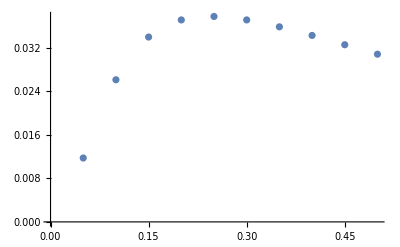

```mathematica
J=1;temp=0.0001;delta=0.1;
ListPlot[Table[{0.05i,delta ds3bandf[J,0.05i,delta]},{i,1,10}]]
```

```mathematica
J=1;temp=0.0001;delta=0.1;
ListPlot[Table[{0.05i,ds3bandftemp[J,0.05i,delta,temp]},{i,1,10}]]
```

-Graphics-

the two completely match!

### J=1, Δ=0.01, μ=0, numerical calculation

```mathematica
(*delta=0.01*)
J=1;delta=0.01;
```

```mathematica
(*SW total*)
mlist=Table[0.001(im-1),{im,1,101}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsgeo3bandf[J,m,delta];
AppendTo[dslist,dstotvalue];
]//Timing
data=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.3125,Null}

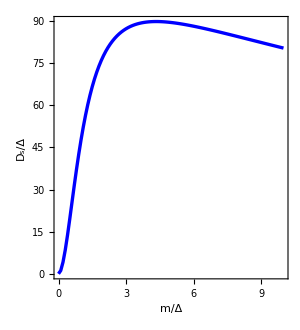

```mathematica
dsvsm=ListPlot[data,
Joined->True,
PlotStyle->{{Thickness[0.008],Blue}},(*PlotRange->{{0,5},{0,0.46}},*)
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},*)
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

### J=1, Δ=0.1 and 0.5, numerical calculation***

```mathematica
(*delta=0.1*)
J=1;delta=0.1;temp=0.0001;
mlist=Table[0.01(im-1)+0.001,{im,1,101}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=ds3bandftemp[J,m,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata01=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.03125,Null}

```mathematica
(*delta=0.5*)
J=1;delta=0.5;
mlist=Table[0.05(im-1)+0.001,{im,1,101}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=ds3bandftemp[J,m,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata05=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.0625,Null}

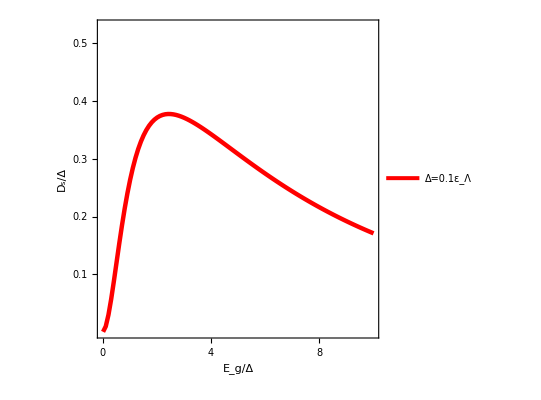

```mathematica
dsvsm01=ListPlot[dsdata01,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,10},{0,0.53}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4,0.5},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.72,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

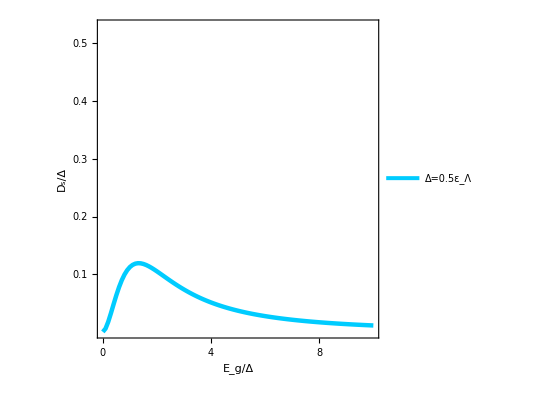

```mathematica
dsvsm05=ListPlot[dsdata05,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},PlotRange->{{0,10},{0,0.53}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4,0.5},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
PlotLegends->Placed[LineLegend[{Style["Δ=0.5ε_Λ",18]}],{0.72,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
Overlay[{dsvsm01,dsvsm05}]
```

-Graphics--Graphics-

### J=6, Δ=0.1 and 0.5, numerical calculation***

```mathematica
(*delta=0.1*)
J=6;delta=0.1;temp=0.0001;
mlist=Table[0.01(im-1)+0.001,{im,1,101}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=ds3bandftemp[J,m,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata01=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.,Null}

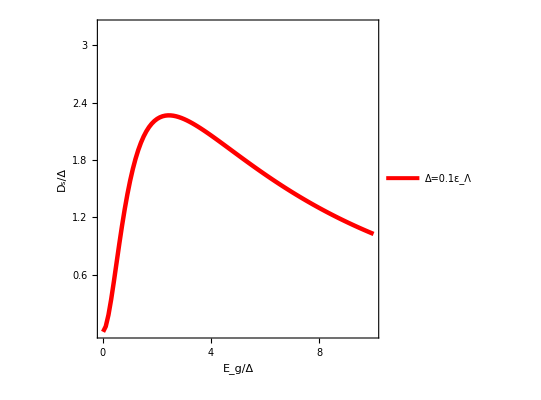

```mathematica
dsvsm01=ListPlot[dsdata01,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,10},{0,3.2}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.6,1.2,1.8,2.4,3},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.28,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
(*delta=0.5*)
J=6;delta=0.5;
mlist=Table[0.05(im-1)+0.001,{im,1,101}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=ds3bandftemp[J,m,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata05=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.,Null}

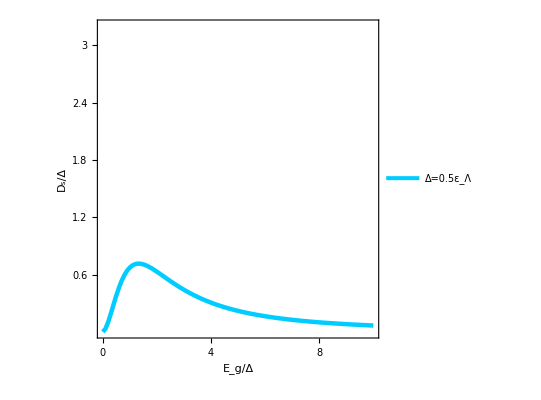

```mathematica
dsvsm05=ListPlot[dsdata05,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},PlotRange->{{0,10},{0,3.2}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.6,1.2,1.8,2.4,3},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
PlotLegends->Placed[LineLegend[{Style["Δ=0.5ε_Λ",18]}],{0.28,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
Overlay[{dsvsm01,dsvsm05}]
```

-Graphics--Graphics-

## 3-dim secant to find Tc

### Def: 3-dim secant method

```mathematica
bkteq3bandf[deltaA_?NumericQ,deltaB_?NumericQ,temp_,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
(π/8)ds3bandftemp[J,m,deltaavg,temp]-temp
)
```

```mathematica
(*input two temps and return a new temp*)
tc3bandfstep[{deltaA0_,deltaB0_,temp0_},{deltaA1_,deltaB1_,temp1_}]:=(
input0={deltaA0,deltaB0,temp0};
input1={deltaA1,deltaB1,temp1};
functionlist={newtonA3bandf,newtonB3bandf,bkteq3bandf};
jacobian=ConstantArray[0,{3,3}];
For[i=1,i<4,i++,
For[j=1,j<4,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],changelist1[[3]],uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],input1[[3]],uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],input1[[3]],uA,uB],{k,1,3}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
tc3bandf[inputdeltaA_,inputdeltaB_,inputtemp_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB,inputtemp};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.98&&outputlist1[[3]]>tcmin,tc3bandfstep[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
temp=outputlist1[[3]]
)
```

```mathematica
J=1;mvalue=0;delta=0.1;tcmin=0.0001;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
m=0.1;temptrial=0.01;
tc3bandf[delta,delta,temptrial]//Timing
```

{0.390625,0.0104468}

### J=1, Δ=0.1 and 0.5 calculation***

```mathematica
{shape1,shape2}=Graphics/@{{Red,Disk[{0,0},0.1]},{RGBColor[0,0.8,1],Polygon[{{0.5,0},{0,0.5},{-0.5,0},{0,-0.5}}]}};
```

```mathematica
J=1;mvalue=0;delta=0.1;tcmin=0.0001;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
mlist=Table[0.025(i-1)+0.01,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.01;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc3bandf[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
tcdata01f=Table[{mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{6.65625,Null}

```mathematica
uA
uB
```

2.51327

2.51327

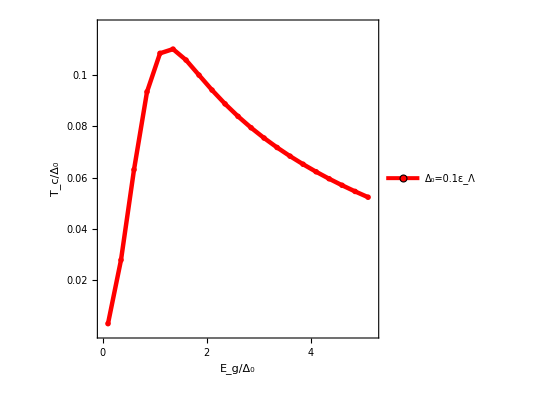

```mathematica
tc01=ListPlot[tcdata01f,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.119}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.02,0.04,0.06,0.08,0.1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
PlotMarkers->{{shape1,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.1ε_Λ",16]}],{0.72,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
J=1;mvalue=0;delta=0.5;tcmin=0.0001;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
mlist=Table[0.125(i-1)+0.05,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.01;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc3bandf[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
tcdata05f=Table[{mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{3.03125,Null}

```mathematica
uA
uB
```

12.5664

12.5664

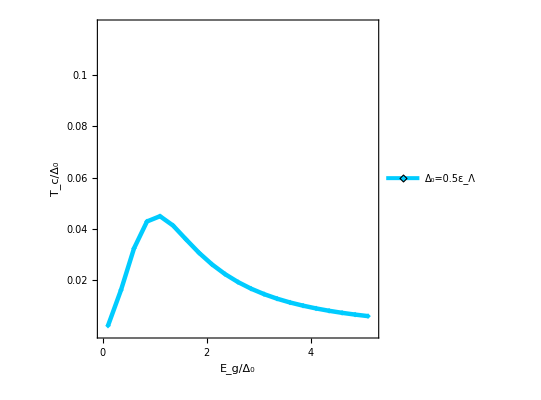

```mathematica
tc05=ListPlot[tcdata05f,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.119}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.02,0.04,0.06,0.08,0.1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
PlotMarkers->{{shape2,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.5ε_Λ",16]}],{0.72,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
Overlay[{tc01,tc05}]
```

-Graphics--Graphics-

```mathematica
Export["tc3bandf.pdf",tcplot]
```

tc3bandf.pdf

### J=6, Δ=0.1 and 0.5 calculation***

```mathematica
{shape1,shape2}=Graphics/@{{Red,Disk[{0,0},0.1]},{RGBColor[0,0.8,1],Polygon[{{0.5,0},{0,0.5},{-0.5,0},{0,-0.5}}]}};
```

```mathematica
J=6;mvalue=0;delta=0.1;tcmin=0.0001;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
mlist=Table[0.025(i-1)+0.01,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.01;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc3bandf[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
tcdata01f=Table[{mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{176.141,Null}

```mathematica
uA
uB
```

2.51327

2.51327

```mathematica
tcdata01f
```

{{0.1,0.0190801},{0.35,0.163932},{0.6,0.27492},{0.85,0.304717},{1.1,0.292369},{1.35,0.265702},{1.6,0.241507},{1.85,0.223352},{2.1,0.21013},{2.35,0.200143},{2.6,0.192304},{2.85,0.185938},{3.1,0.180618},{3.35,0.176061},{3.6,0.172076},{3.85,0.168527},{4.1,0.165318},{4.35,0.162376},{4.6,0.159646},{4.85,0.157089},{5.1,0.154669}}

```mathematica
tcdata01f={{0.1,0.019080107684386848},{0.35000000000000003,0.1639323877213136},{0.6000000000000001,0.27491989428691577},{0.8500000000000001,0.30471741524862284},{1.1,0.2923692134508335},{1.35,0.2657015065648746},{1.6000000000000003,0.241507419404964},{1.8500000000000003,0.22335155287518654},{2.1,0.21013018101643705},{2.35,0.20014298439174388},{2.6,0.19230366222254208},{2.8500000000000005,0.18593809928294316},{3.1000000000000005,0.18061786092329477},{3.35,0.17606106198144655},{3.6000000000000005,0.17207574551859534},{3.85,0.16852706340248172},{4.1000000000000005,0.16531766416098662},{4.3500000000000005,0.16237557650521958},{4.6000000000000005,0.15964648195408773},{4.8500000000000005,0.15708864141435058},{5.1,0.15466947600127676}};
```

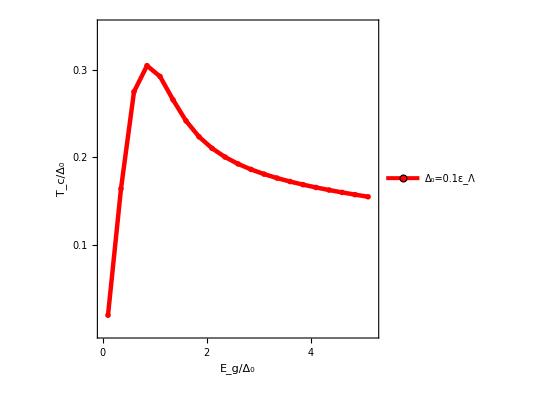

```mathematica
tc01=ListPlot[tcdata01f,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.35}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
PlotMarkers->{{shape1,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.1ε_Λ",16]}],{0.72,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
J=6;mvalue=0;delta=0.5;tcmin=0.0001;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
mlist=Table[0.125(i-1)+0.05,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.05;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc3bandf[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
tcdata05f=Table[{mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{103.344,Null}

```mathematica
uA
uB
```

12.5664

12.5664

```mathematica
tcdata05f
```

{{0.1,0.0130739},{0.35,0.0976506},{0.6,0.183079},{0.85,0.217431},{1.1,0.213603},{1.35,0.194078},{1.6,0.172139},{1.85,0.152786},{2.1,0.135988},{2.35,0.121175},{2.6,0.107951},{2.85,0.0961043},{3.1,0.0855298},{3.35,0.0761617},{3.6,0.0681607},{3.85,0.0609167},{4.1,0.0546241},{4.35,0.0491756},{4.6,0.0444531},{4.85,0.040348},{5.1,0.0367656}}

```mathematica
tcdata05f={{0.1,0.013073871811950587},{0.35,0.0976506261442666},{0.6,0.1830786815494289},{0.85,0.21743114426903543},{1.1,0.21360322354292727},{1.35,0.1940780937941106},{1.6,0.17213935012350626},{1.85,0.1527862058174449},{2.1,0.13598829196040077},{2.35,0.12117508906722131},{2.6,0.10795098742445389},{2.85,0.09610428576285322},{3.1,0.08552981622964102},{3.35,0.07616168818259138},{3.6,0.06816066815184955},{3.85,0.06091674470321345},{4.1,0.05462409460709242},{4.35,0.04917557556584204},{4.6,0.044453059979587047},{4.85,0.04034798865895707},{5.1,0.03676558602695389}};
```

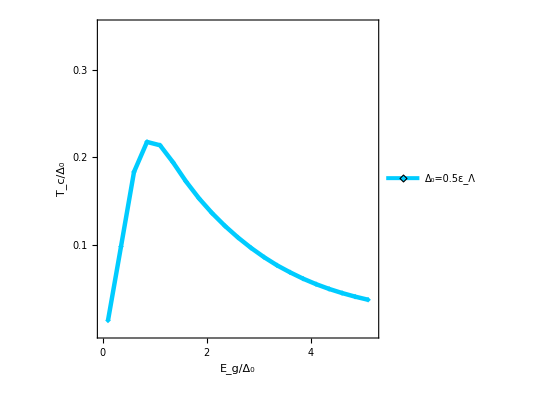

```mathematica
tc05=ListPlot[tcdata05f,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.35}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
PlotMarkers->{{shape2,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.5ε_Λ",16]}],{0.72,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
Overlay[{tc01,tc05}]
```

-Graphics--Graphics-

```mathematica
Export["tc3bandf.pdf",tcplot]
```

tc3bandf.pdf

### other plots

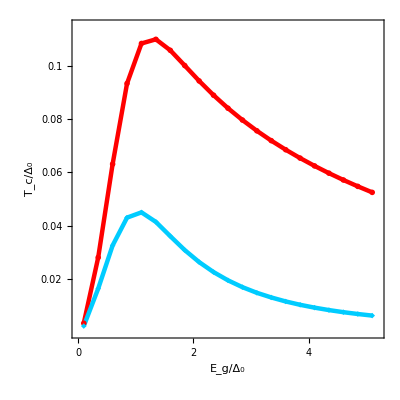

```mathematica
tcfcombine=ListPlot[{tcdata01f,tcdata05f},
Joined->True,
PlotStyle->{{Red,Thickness[0.008]},{RGBColor[0,0.8,1],Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.115}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",23],Style["T_c/Δ_0",23]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.02,0.04,0.06,0.08,0.1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 22],
PlotMarkers->{{shape1,0.03},{shape2,0.03}},
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

## 2-dim secant to find T=0 SC gap vs Eg

### Def: T=0 secant for SC gap

```mathematica
newtonA3bandft0[deltaA_?NumericQ,deltaB_?NumericQ,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
(uA/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2 /(2quasiplusf[m,deltaavg])+Abs[u0[J,m,k,phi][[1]]]^2/(2quasi0f[m,deltaavg])+Abs[uminus[J,m,k,phi][[1]]]^2/(2quasiminusf[m,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaA
)
```

```mathematica
newtonB3bandft0[deltaA_?NumericQ,deltaB_?NumericQ,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
(uB/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2 /(2quasiplusf[m,deltaavg])+Abs[u0[J,m,k,phi][[2]]]^2/(2quasi0f[m,deltaavg])+Abs[uminus[J,m,k,phi][[2]]]^2/(2quasiminusf[m,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaB
)
```

```mathematica
secant3bandfstept0[{deltaA0_,deltaB0_},{deltaA1_,deltaB1_}]:=(
input0={deltaA0,deltaB0};
input1={deltaA1,deltaB1};
functionlist={newtonA3bandft0,newtonB3bandft0};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],uA,uB],{k,1,2}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
secant3bandft0[inputdeltaA_,inputdeltaB_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.95&&inputdeltaA>tcmin,secant3bandfstept0[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
)
```

### J=6, Δ=0.1 and 0.5, T=0 SC gap vs Eg***

```mathematica
{shape1,shape2}=Graphics/@{{Red,Disk[{0,0},0.1]},{RGBColor[0,0.8,1],Polygon[{{0.5,0},{0,0.5},{-0.5,0},{0,-0.5}}]}};
```

```mathematica
J=6;mvalue=0;delta=0.1;tcmin=0.0001;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
mlist=Table[0.025(i-1)+0.005,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
deltalist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
secant3bandft0[deltaAtrial,deltaBtrial];
AppendTo[deltalist,(2deltaA+deltaB)/3];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
]//Timing
data01f=Table[{mlist[[i]]/delta,deltalist[[i]]/delta},{i,1,Length@mlist}];
```

{19.5781,Null}

```mathematica
uA
uB
```

2.51327

2.51327

```mathematica
data01f
```

{{0.05,0.999168},{0.3,0.971128},{0.55,0.902722},{0.8,0.807096},{1.05,0.705505},{1.3,0.620813},{1.55,0.559881},{1.8,0.517584},{2.05,0.487607},{2.3,0.466575},{2.55,0.449606},{2.8,0.436339},{3.05,0.425754},{3.3,0.417123},{3.55,0.409954},{3.8,0.403908},{4.05,0.398742},{4.3,0.394277},{4.55,0.39038},{4.8,0.38695},{5.05,0.383908}}

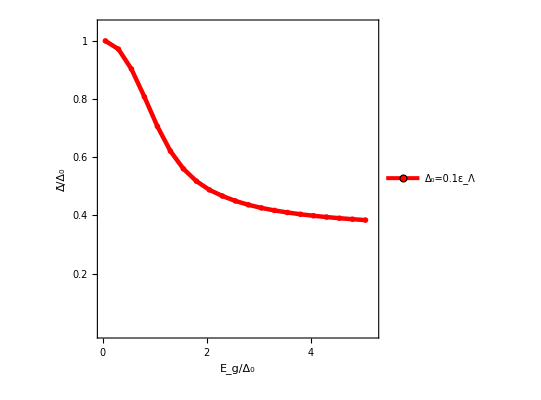

```mathematica
gap01f=ListPlot[data01f,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,5.2},{0,1.05}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["Δ̄/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
PlotMarkers->{{shape1,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.1ε_Λ",16]}],{0.72,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
J=6;mvalue=0;delta=0.5;tcmin=0.0001;
uA=uaf[J,mvalue];
uB=ubf[J,mvalue];
mlist=Table[0.125(i-1)+0.025,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
deltalist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
secant3bandft0[deltaAtrial,deltaBtrial];
AppendTo[deltalist,(2deltaA+deltaB)/3];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
]//Timing
data05f=Table[{mlist[[i]]/delta,deltalist[[i]]/delta},{i,1,Length@mlist}];
```

{106.016,Null}

```mathematica
uA
uB
```

12.5664

12.5664

```mathematica
data05f
```

{{0.05,0.999171},{0.3,0.971086},{0.55,0.902731},{0.8,0.807164},{1.05,0.705618},{1.3,0.620875},{1.55,0.559897},{1.8,0.517586},{2.05,0.489131},{2.3,0.466585},{2.55,0.449488},{2.8,0.436223},{3.05,0.425652},{3.3,0.417036},{3.55,0.409881},{3.8,0.403846},{4.05,0.398689},{4.3,0.394232},{4.55,0.390342},{4.8,0.386918},{5.05,0.38388}}

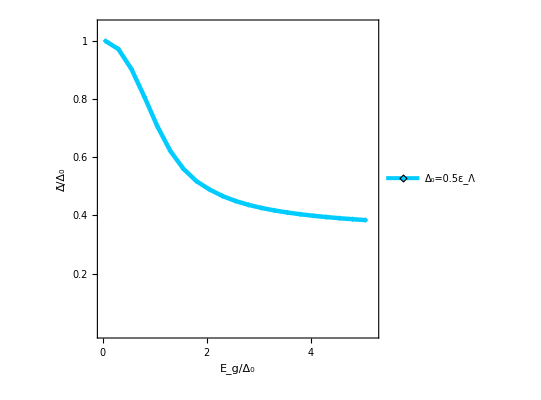

```mathematica
gap05f=ListPlot[data05f,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},PlotRange->{{0,5.2},{0,1.05}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["Δ̄/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
PlotMarkers->{{shape2,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.5ε_Λ",16]}],{0.72,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
Overlay[{gap01f,gap05f}]
```

-Graphics--Graphics-